```mathematica
si=getSi[1]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
s12=scalar[1,2,{1,2}];
```

```mathematica
Tr[s12]
```

0

```mathematica
i2=KP[si,si];
```

```mathematica
τ=i2+bs s12+bt(s12.s12-4/3 i2);
```

```mathematica
ρ=1/9(i2+as s12+at(s12.s12-4/3 i2));
```

```mathematica
Clear[as]
```

```mathematica
Clear[at]
```

```mathematica
{As,At}=Solve[ρ==τ.τ/Tr[τ.τ],{as,at}][[1]]//Simplify
```

{as→-(6 bs (-3+bt))/(9+12 bs^2-12 bs bt+8 bt^2),at→(3 (3 bs^2-12 bs bt+bt (6+7 bt)))/(9+12 bs^2-12 bs bt+8 bt^2)}

```mathematica
As=As/.(as->x_):>x
```

-(6 bs (-3+bt))/(9+12 bs^2-12 bs bt+8 bt^2)

```mathematica
At=At/.(at->x_):>x
```

(3 (3 bs^2-12 bs bt+bt (6+7 bt)))/(9+12 bs^2-12 bs bt+8 bt^2)

```mathematica
dss=D[As,bs]//Simplify
```

-(6 (-3+bt) (9-12 bs^2+8 bt^2))/((9+12 bs^2-12 bs bt+8 bt^2)^2)

```mathematica
dst=D[As,bt]//Simplify
```

-(6 bs (9-36 bs+12 bs^2+48 bt-8 bt^2))/((9+12 bs^2-12 bs bt+8 bt^2)^2)

```mathematica
dts=D[At,bs]//Simplify
```

(18 (18 bs^2 bt-2 (-3+bt)^2 bt+bs (9-24 bt-20 bt^2)))/((9+12 bs^2-12 bs bt+8 bt^2)^2)

```mathematica
dtt=D[At,bt]//Simplify
```

-(18 (-9+18 bs^3-21 bt+8 bt^2-4 bs^2 (3+5 bt)-2 bs (-9+bt^2)))/((9+12 bs^2-12 bs bt+8 bt^2)^2)

```mathematica
Det[{{dss, dst}, {dts, dtt}}]//Simplify
```

(108 (54 bs^3-6 bs (-3+bt)^2-9 bs^2 (3+8 bt)+(-3+bt)^2 (3+8 bt)))/((9+12 bs^2-12 bs bt+8 bt^2)^3)

```mathematica
(6bs-3-8bt)(3bs+3-bt)(3bs-3+bt)//Expand//Simplify
```

54 bs^3-6 bs (-3+bt)^2-9 bs^2 (3+8 bt)+(-3+bt)^2 (3+8 bt)

```mathematica
P0=i2;
```

```mathematica
Tr[P0]
```

9

```mathematica
PositiveSemidefiniteMatrixQ[P0]
```

True

```mathematica
s1212=s12.s12-4/3 i2;
```

```mathematica
P1=2/3(i2+3/4 s12+3/4 s1212);
```

```mathematica
P1.P1==P1
```

True

```mathematica
Tr[P1]
```

6

```mathematica
PositiveSemidefiniteMatrixQ[P6]
```

False

```mathematica
P2=8/9(i2-3/8 s1212);
```

```mathematica
P2.P2==P2
```

True

```mathematica
Tr[P2]
```

8

```mathematica
P3=4/9(i2-9/8 s12 - 3/8 s1212);
```

```mathematica
P3.P3==P3
```

True

```mathematica
Tr[P3]
```

4

```mathematica
P4=5/9(i2+9/10 s12+3/10 s1212);
```

```mathematica
P4.P4==P4
```

True

```mathematica
Tr[P4]
```

5

```mathematica
P5 = 1/3(i2-3/2 s12-3/2 s1212);
```

```mathematica
P5.P5==P5
```

True

```mathematica
Tr[P5]
```

3

```mathematica
P6=1/9(i2+3 s1212);
```

```mathematica
P6.P6==P6
```

True

```mathematica
Tr[P6]
```

1

```mathematica
{p0,p1,p2,p3,p4,p5,p6}={{8/3,0},{3/4,3/4},{0,-3/8},{-9/8,-3/8},{9/10,3/10},{-3/2,-3/2},{0,3}}
```

{{8/3,0},{3/4,3/4},{0,-3/8},{-9/8,-3/8},{9/10,3/10},{-3/2,-3/2},{0,3}}

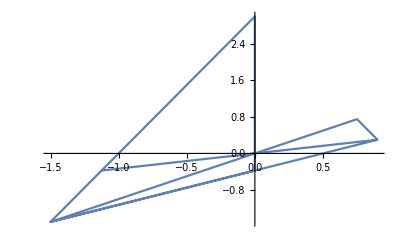

```mathematica
ListLinePlot[{p4,p5,p6,p2,p5,p1,p4,p3}]
```